```mathematica
g = 9.8; (*Gravity constant*)
l = 0.5; (*Length of the pendulum*)

θ0 = (20 × π) / 180; (*20 degreen in radians*)
ω0 = 0; (*Starting from rest*)

ode1 = {θ''[t] == - (g/l)*Sin[θ[t]], θ[0] == θ0, θ'[0] == ω0};
sol = NDSolve[ode1, θ, {t, 0, 20}];

myplot1 = Plot[(180/π) θ[t] /. sol, {t, 0, 20}, PlotStyle -> RGBColor[0, 0, 1], PlotRange -> All];

omega = √(g/l);
approx = (180 / π) θ0 Cos[omega * t];
myplot2 = Plot[approx, {t, 0, 20}, PlotStyle -> RGBColor[1, 0, 0], PlotRange -> All];
```

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

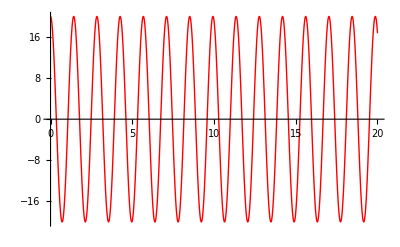

```mathematica
Show[{myplot1, myplot2}]
```

```mathematica
Manipulate[
g = 9.8; l = 0.5; omega = √(g/l);
Module[
{result = NDSolve[{θ''[t] == -(g/l) * Sin[θ[t]], θ[0] == θ0, θ'[0] == ω0}, θ, {t, 0, 20}]},
Plot[{(180 / π) θ0 Cos[omega * t], (180/π) * θ[t] /. result}, {t, 0, 20}, PlotStyle -> {{Blue}, {Dashed, Red}},  PlotRange -> All,AxesLabel -> {"t (s)", "θ (rad)"}, PlotRange -> {{0, 20}, {-20, 20}}, ImageSize -> {500, 300}]],
{{l, 0.5, "Length (m)"}, 0, 2, Appearance -> "Labeled"},
{{θ0, 20 * π/180, "Initial Angle (rad)"}, 0.1, π/2, Appearance -> "Labeled"},
{{ω0, 0, "Initial Speed (rad/s)"}, 0, 10.0, Appearance -> "Labeled"}]
```

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.349066, True}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
(*x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]*)
(*y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2])*)
V  = 30
θ  = (50 × π) / 180
c = 3 10^8
g = 9.8
(*vt = Sqrt[(m g)/c]*)
vt = 135
sol = NDSolve[ {x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0]==0.0,x'[0]==V Cos[θ],y[0]==2,y'[0]==V Sin[θ]}, {x, y}, {t, 0, 200} ]
```

30

(5 π)/18

300000000

9.8

135

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

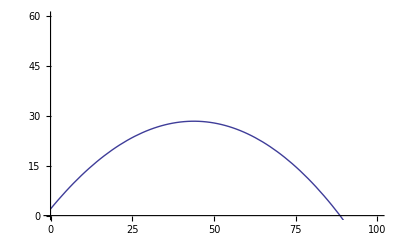

```mathematica
myplot = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200},PlotRange-> {{0,100},{0,60}}]
```

```mathematica
Manipulate[
g = 9.8,
Module[{result=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),
x[0]==0.0,x'[0]==v0 Cos[θ],y[0]==2,y'[0]==v0 Sin[θ]},{x,y},{t,0,200}]},

ParametricPlot[ { { {v0 Cos[θ] t},{h0+v0 Sin[θ] t-(1/2) g t^2},{t,0,200}},{ {Evaluate[ {x[t],y[t] }/.result] },{t,0,200} } },ImageSize -> {500,300},AxesLabel-> {"x (m)","y (m)"},PlotStyle->{{Blue},{Red}},PlotRange->All]],

{{v0,30,"Initial Velocity (m/s)"},0,10,Appearance->"Labeled"},
{{θ,50*π/180,"Launch Angle (rad)"},0.01,π/2,Appearance->"Labeled"},{{vt,135,"Terminal Velocity (m/s)"},0.5,150.0,Appearance->"Labeled"},
{{h0, 0,"Launch Height (m)"},0,2,Appearance -> "Labeled"},
{{t,0.01,"Time (s)"},0,200,Appearance->"Labeled"}]
```

Manipulate::vsform: Manipulate argument {result = NDSolve[{SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == Times[« 2 »], SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == Times[« 2 »], x[« 1 »] == 0.`, SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == Times[« 2 »], y[« 1 »] == 2, SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == Times[« 2 »]}, {x, y}, {t, 0, 200}]}, ParametricPlot[{{{v0 Cos[« 1 »] t}, {h0 + Times[« 3 »] + Times[« 2 »]}, {t, 0, 200}}, {{Evaluate[ReplaceAll[« 2 »]]}, {t, 0, 200}}}, « 3 », PlotRange → All] does not have the correct form for a variable specification.

Manipulate[g=9.8,Module[{result=NDSolve[{x''[t]==-((g x'[t]) √(x'[t]^2+y'[t]^2))/vt^2,y''[t]==-g (1+(y'[t] √(x'[t]^2+y'[t]^2))/vt^2),x[0]==0.,x'[0]==v0 Cos[θ],y[0]==2,y'[0]==v0 Sin[θ]},{x,y},{t,0,200}]},ParametricPlot[{{{v0 Cos[θ] t},{h0+v0 Sin[θ] t-(g t^2)/2},{t,0,200}},{{Evaluate[{x[t],y[t]}/.result]},{t,0,200}}},ImageSize→{500,300},AxesLabel→{x (m),y (m)},PlotStyle→{{Blue},{Red}},PlotRange→All]],{{v0,30,Initial Velocity (m/s)},0,10,Appearance→Labeled},{{θ,(50 π)/180,Launch Angle (rad)},0.01,π/2,Appearance→Labeled},{{vt,135,Terminal Velocity (m/s)},0.5,150.,Appearance→Labeled},{{h0,0,Launch Height (m)},0,2,Appearance→Labeled},{{t,0.01,Time (s)},0,200,Appearance→Labeled}]